## Pristine ZrC electron transport;

```mathematica
Some basic information;
```

```mathematica
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850};
tempps={0,10,300,500,760,1000,1500,1900,2500,3200,3800};
temppps=tempps[[2;;11]];
temps2={300,300,760,1900,2500,3200,3800};
temps3={300,760,1900,2500,3200,3800};
THz2meV=1/4.135665538536;K2meV=0.086173324;kjmol2evatom=1/(96.487*64);
Nat=64;Natvac=63;mass={91.224,12.0107,1};
ang2bohr=1/0.529177208;ev2har=1/27.211396;kB=1000*8.617332478*10^−5;
eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
(*Constant, Fermi-Dirac and Fermi-Dirac changing with energy*)
K2eV=8.617332478*10^−5;
fermiDirac[energy_,temp_]:=1/(Exp[energy/(K2eV*temp)]+1)
(*define sigma and8 kappa kernels*)
(*temp in energy units*)
sigmaK[energy_,temp_]:=-D[fermiDirac[energy,temp],energy]
kappaK[energy_,temp_]:=-(1/temp)*(energy^2)*D[fermiDirac[energy,temp],energy]
eV2ryd=1/13.605698066;ryd2eV=13.605698066;
```

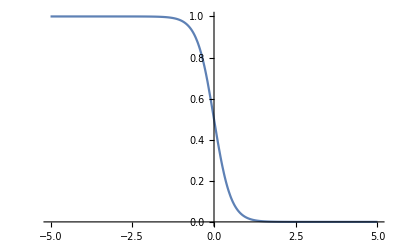

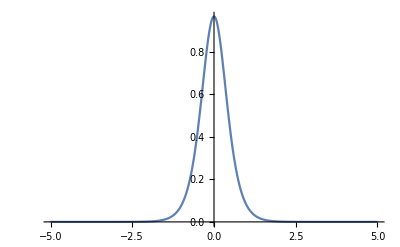

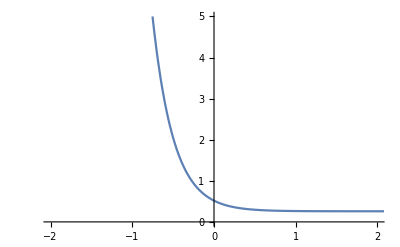

```mathematica
Plot[fermiDirac[e,3000],{e,-5,5}]
Plot[Evaluate@sigmaK[e,3000],{e,-5,5},PlotRange->All]
Plot[Evaluate[fermiDirac[e,3000]/Evaluate@sigmaK[e,3000]],{e,-5,5},PlotRange->{{-2,2},{0,5}}]
Integrate[Evaluate@sigmaK[e,3000],{e,-5,5}]
```

```mathematica
Import data;
SetDirectory["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/"];
temps={"0K","10K","300K","500K","760K","1000K","1500K","1900K","2500K","3200K","3800K"};
scatteringRates=Table[ReadList[StringJoin["Variable_Volume/ScatteringRates/constant_smearing/kRandom/",ToString@temps[[i]],"/scattering_rate",ToString@temps[[i]]],{Number, Number,Number, Number,Number}],{i,1,11}];
```

#### List of energy vs rate or lifetime;

```mathematica
lifeData=Table[Transpose[{Transpose[scatteringRates[[1]]][[3]],Transpose[scatteringRates[[i]]][[5]]}],{i,1,11}];
rateData=Table[Transpose[{Transpose[scatteringRates[[i]]][[3]],Transpose[scatteringRates[[i]]][[4]]}],{i,1,11}];
```

#### Plot rate 1/τ ;

```mathematica
ListPlot[lifeData[[1]],PlotRange->{All,{0,3*10^-9}}]
```

-Graphics-

```mathematica
Plot lifetime τ ;
```

```mathematica
ListPlot[rateData[[1]],PlotRange->{All,{0,6*10^14}}]
```

-Graphics-

#### Randomly sample τ;

```mathematica
rateDataR6=Table[RandomSample[rateData[[i]],100000],{i,1,11}];
rateDataR5=Table[RandomSample[rateData[[i]],10000],{i,1,11}];
rateDataR4=Table[RandomSample[rateData[[i]],1000],{i,1,11}];
rateDataR3=Table[RandomSample[rateData[[i]],100],{i,1,11}];
```

```mathematica
ListPlot[Table[rateDataR5[[i]],{i,2,11,2}],PlotLegends->SwatchLegend[Table[temps[[i]],{i,2,11,2}]],Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"},PlotRange->{All,{0,6*10^15}}]
```

-Graphics-

```mathematica
nasdaq=FinancialData["NASDAQ:AAPL",All,"Value"];
data=Log[Most[nasdaq]/Rest[nasdaq]];
```

```mathematica
rateDataR3[[1]][[1]]
```

{-4.93251,1.44806×10^13}

```mathematica
Table[rateDataR3[[1]][[i]],{i,1,Length[rateData3]}]
```

{}

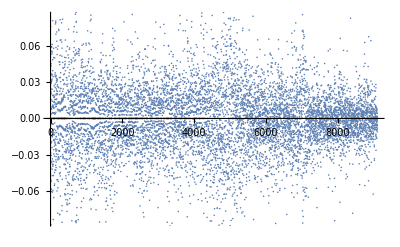

```mathematica
ListPlot@data
```

```mathematica
rateDataR3[[1]]
```

{{5.19271,8.75388×10^13},{5.71902,3.57755×10^13},{-0.786334,8.35856×10^13},{0.946092,9.67423×10^13},{3.50971,1.10391×10^14},{-2.5366,2.09265×10^14},{5.01233,8.0559×10^13},{-1.80254,1.3697×10^14},{-2.2117,2.94792×10^14},{-2.18458,2.43655×10^14},{2.50357,1.00139×10^14},{5.29184,8.74271×10^13},{-1.08996,7.5019×10^13},{5.15518,1.12792×10^14},{4.39607,6.82129×10^13},{-4.47752,3.13896×10^13},{-4.15588,4.38452×10^13},{4.9698,6.01761×10^13},{-0.0332913,1.68391×10^13},{-2.41514,2.92372×10^14},{-2.29771,2.64207×10^14},{-2.29476,2.33886×10^14},{-4.0887,4.55903×10^13},{-2.23497,2.06498×10^14},{-2.4587,3.43784×10^14},{3.44934,1.40147×10^14},{-2.06527,1.71667×10^14},{2.39983,1.26662×10^14},{1.97513,9.94113×10^13},{-2.40755,3.51311×10^14},{3.8469,1.00912×10^14},{4.33326,1.06904×10^14},{-0.486498,5.05368×10^13},{-3.93752,4.26195×10^13},{-1.54708,1.26968×10^14},{4.6833,4.82773×10^13},{0.734684,7.55446×10^13},{-2.21148,2.43589×10^14},{-4.44779,3.26902×10^13},{-2.11502,239343464423156},{1.5014,9.69064×10^13},{-1.32202,8.77169×10^13},{4.84825,7.16111×10^13},{-2.59874,2.16743×10^14},{-3.86506,4.60841×10^13},{3.08764,1.17644×10^14},{0.228529,7.6777×10^13},{-2.29608,2.13581×10^14},{2.05568,9.47962×10^13},{-3.65795,5.55191×10^13},{-2.21209,1.9017×10^14},{4.83105,6.34903×10^13},{5.76493,3.411×10^13},{-2.11269,2.23922×10^14},{4.08714,9.08383×10^13},{-2.31336,3.88012×10^14},{-3.85625,4.92033×10^13},{-1.4806,1.07252×10^14},{5.73014,4.36563×10^13},{4.112,9.49463×10^13},{-2.82036,9.5798×10^13},{5.72618,4.32052×10^13},{0.405162,7.64003×10^13},{-2.37831,2.36754×10^14},{-2.98319,5.28848×10^13},{-3.54844,4.76022×10^13},{-1.72798,1.27439×10^14},{-3.54514,4.98479×10^13},{1.74318,9.32861×10^13},{4.64275,8.83527×10^13},{0.7779,9.4112×10^13},{5.68297,4.47246×10^13},{5.14183,6.29873×10^13},{-2.19979,2.74877×10^14},{2.02108,1.17816×10^14},{0.56335,7.89584×10^13},{1.59633,1.1178×10^14},{5.24987,9.13936×10^13},{-3.5908,5.44855×10^13},{-3.76936,5.32237×10^13},{-2.30303,3.19708×10^14},{4.94649,7.41805×10^13},{3.13977,1.09136×10^14},{-3.37421,4.92696×10^13},{3.19412,1.14992×10^14},{-2.41198,3.27777×10^14},{3.71146,1.22799×10^14},{-3.50767,5.20868×10^13},{5.41312,6.94955×10^13},{5.10422,1.14459×10^14},{-1.78575,1.53516×10^14},{-2.37831,3.25215×10^14},{5.36675,8.84823×10^13},{3.95098,1.22062×10^14},{-2.17462,2.38957×10^14},{-2.89879,7.67555×10^13},{-2.57225,1.66619×10^14},{5.19061,9.73876×10^13},{4.68287,9.03785×10^13},{-0.437654,4.78628×10^13}}

```mathematica
dataT=Transpose[rateDataR3[[1]][[1;;100]]];
data=rateDataR3[[1]][[1;;10]];
CorrelationDistance[data[[1]],data[[2]]]
```

0.

```mathematica
𝒟=Smoot
```

{{5.19271,5.71902,-0.786334,0.946092,3.50971,-2.5366,5.01233,-1.80254,-2.2117,-2.18458},{8.75388×10^13,3.57755×10^13,8.35856×10^13,9.67423×10^13,1.10391×10^14,2.09265×10^14,8.0559×10^13,1.3697×10^14,2.94792×10^14,2.43655×10^14}}

```mathematica
Transpose[rateDataR3[[1]][1;;10][[1]]]
```

Transpose[1;;10]

```mathematica
rateDataR3;
𝒟=SmoothKernelDistribution[Transp]]]
```

$Aborted

```mathematica
Plot[Evaluate@PDF[𝒟,x],{x,-10,10},PlotRange->All]
```

-Graphics-

```mathematica
data
```

{0.0688242,0.746552,0.935411,0.0981192,0.291368,0.0703937,0.365902,0.136298,0.683827,0.146975,9980,0.144574,0.67811,0.0719684,0.0582874,1.44947,0.325278,0.82569,0.0116123,0.0177213,0.530172}
 |  |  |  |

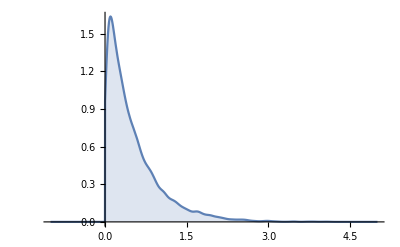

```mathematica
data=RandomVariate[ExponentialDistribution[2],10^4];
dist=SmoothKernelDistribution[data];
𝒟=TruncatedDistribution[{0,Infinity},dist];
Plot[PDF[𝒟,x]//Evaluate,{x,-1,5},PlotRange->All,Filling->Axis]
```

#### Lifetime data and moving mean;

```mathematica
Show[Table[{ListPlot[rateDataR5[[i]],PlotRange->{All,{0,6*10^15}},Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"},ImageSize->600],ListPlot[MovingMap[Mean,{rateDataR5[[i]]},0.11],PlotStyle->Red]},{i,1,11,3}]]
```

-Graphics-

```mathematica
Gaussian process model;
```

```mathematica
rateDataR4GP=Flatten[{#1->#2}&@@@rateDataR4[[1]]];
p4=Predict[rateDataR4GP,Method->"GaussianProcess"];
```

$Aborted

```mathematica
Show[Plot[{p4[x],p4[x]+StandardDeviation[p4[x,"Distribution"]],p4[x]-StandardDeviation[p4[x,"Distribution"]]},{x,-5,5},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"},Frame->True,FrameLabel->{"E-E_F(eV)","1/τ (s)"},ImageSize->600,PlotRange->{{-5,5},{0,4*10^14}}],ListPlot[List@@@rateDataR4GP,PlotStyle->Red,PlotLegends->{"Data"}]]
```

$Aborted

```mathematica
Interpolate tau in energy;
```

```mathematica
interTau=Table[Interpolation[MovingMap[Mean,{rateDataR5[[i]]},0.11],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
Plot tau;
```

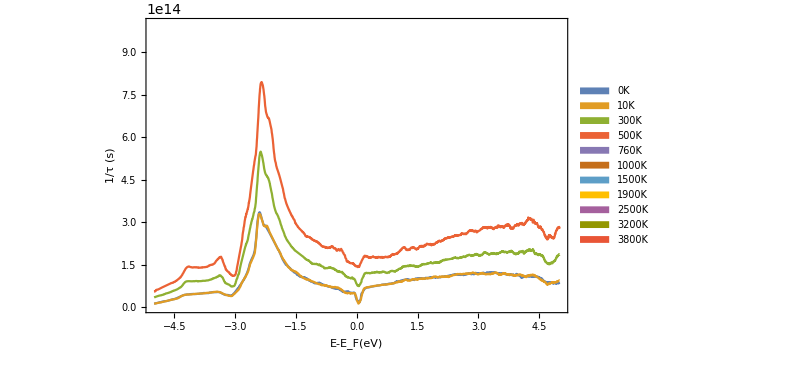

```mathematica
Plot[Evaluate@Table[interTau[[i]][x],{i,1,11}],{x,-5,5},PlotLegends->SwatchLegend[temps],Frame->True,FrameLabel->{"E-E_F(eV)","1/τ (s)"},ImageSize->600,PlotRange->{All,{0,8*10^15}}]
```

```mathematica
interTau[[1]][x]
```

InterpolatingFunction[{{-5.33485, 5.79071}}, <>][x]

```mathematica
Plot tau times the charge transport distribution function;
```

Part::pkspec1: The expression i cannot be used as a part specification.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

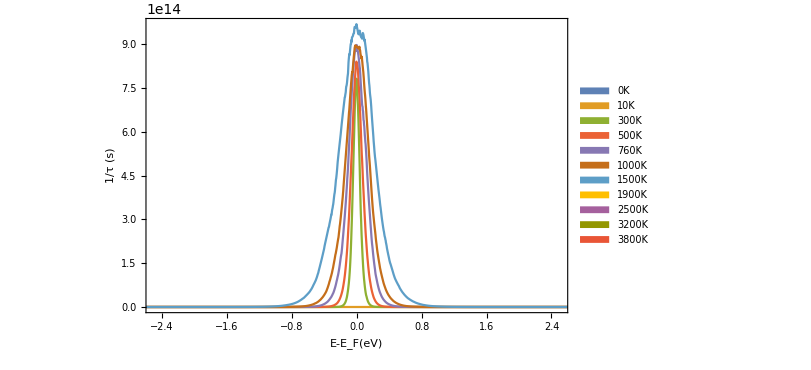

```mathematica
Plot[Evaluate@Table[Evaluate[sigmaK[x,tempps[[i]]]*interTau[[i]][x]],{i,1,11}],{x,-5,5},PlotLegends->SwatchLegend[temps],Frame->True,FrameLabel->{"E-E_F(eV)","1/τ (s)"},ImageSize->600,PlotRange->{{-2.5,2.5},All}]
```

```mathematica
Calculate average tau over 1 and over the kappa kernel;
```

```mathematica
upper=5;lower=-5;
mean55rate=Table[(1/NIntegrate[1,{energy,-5,5}])*NIntegrate[interTau[[i]][energy],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
(*Note delta_T=1 added to the integral over f' to make it stable*)
mean55rateFD=Table[(1/NIntegrate[sigmaK[energy,tempps[[i]]+1],{energy,-5,5}])*NIntegrate[interTau[[i]][energy]*sigmaK[energy,tempps[[5]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

{9.61675×10^13,1.63521×10^14,2.44506×10^14,3.64295×10^14,4.75761×10^14,7.23488×10^14,9.28406×10^14,1.26758×10^15,1.70569×10^15,2.1702×10^15}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.499952 and 0.0292532 for the integral and error estimates.

{7.63108×10^13,9.2237×10^13,1.53022×10^14,2.44925×10^14,3.23533×10^14,5.11331×10^14,6.65232×10^14,9.2939×10^14,1.28669×10^15,1.68336×10^15}

```mathematica
tmean55tau=Transpose[{temppps,1/mean55rate}];
tmean55tauFD=Transpose[{temppps,1/mean55rateFD}];
(*Interpolation*)
tmean55tauinter=Interpolation[tmean55tau,InterpolationOrder->3];
tmean55tauFDinter=Interpolation[tmean55tauFD,InterpolationOrder->3];
```

```mathematica
Plot average tau over 1;
```

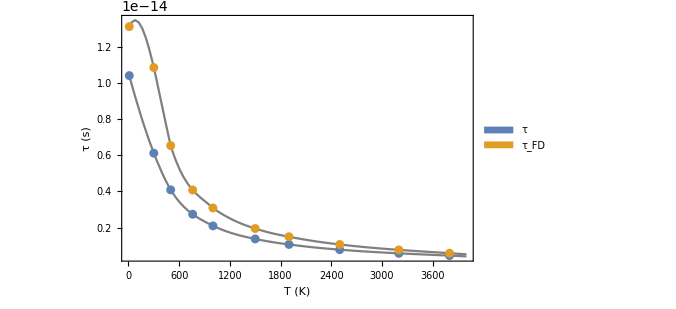

```mathematica
Show[Plot[Evaluate[{tmean55tauinter[x],tmean55tauFDinter[x]}],{x,0,4000},PlotRange->{{0,4000},All},PlotStyle->Gray,Frame->True,FrameLabel->{"T (K)","τ (s)"},ImageSize->500],ListPlot[{tmean55tau,tmean55tauFD},PlotLegends->SwatchLegend[{"τ","τ_FD"}]]]
```

```mathematica
Plot average tau over sigma kernel;
```

```mathematica
tmean55rate=Transpose[{temppps,mean55rate}];
tmean55rateFD=Transpose[{temppps,mean55rateFD}];
Show[Plot[Evaluate[{Interpolation[tmean55rate][x],Interpolation[tmean55rateFD][x]}],{x,0,4000},PlotRange->{{0,4000},All},PlotStyle->Gray,Frame->True,FrameLabel->{"T (K)","τ (s)"},ImageSize->500],ListPlot[{tmean55rate,tmean55rateFD},PlotLegends->SwatchLegend[{"τ","τ_FD"}]]]
```

-Graphics-

```mathematica
Plot  tau times sigma kernel;
```

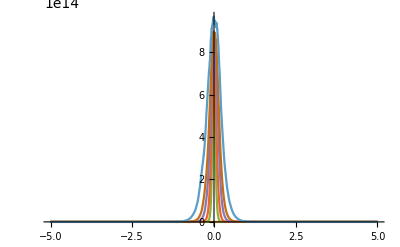

```mathematica
Plot[Evaluate@Table[Evaluate[sigmaK[x,tempps[[i]]]*interTau[[i]][x]],{i,1,11}],{x,-5,5},PlotRange->All]
```

```mathematica
Import DOS;
```

```mathematica
(*Mermin+QHA*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/OUT_ZrC_Mermin_QHA_PERF_KP191919"];
filesDOSperfMermin={"4667_000_000.hte.transdos", "4667_000_026.hte.transdos", "4671_300_026.hte.transdos", "4685_760_065.hte.transdos", "4731_1900_164.hte.transdos", "4760_2500_215.hte.transdos", "4802_3200_276.hte.transdos", "4848_3800_327.hte.transdos"};
(*Exclude the DOS with zero smearing*)
importedDOSperfMermin=Table[ReadList[filesDOSperfMermin[[i]],{Word,Word,Word}],{i,2,8}];
(*QHA*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/OUT_ZrC_QHA_fixedTel_PERF_KP191919"];
filesDOSperf={"46583_SP_COND_252525.hte.transdos", "4685_SP_COND_252525.hte.transdos", "4730_SP_COND_252525.hte.transdos", "4759_SP_COND_252525.hte.transdos", "4801_SP_COND_252525.hte.transdos", "4850_SP_COND_252525.hte.transdos"};
importedDOSperf=Table[ReadList[filesDOSperf[[i]],{Word,Word,Word}],{i,1,6}];
```

```mathematica
Parse DOS;
```

```mathematica
(*Mermin+QHA*)
perfDOSM=Table[Transpose@{Table[ryd2eV*Internal`StringToDouble[importedDOSperfMermin[[j]][[i]][[1]]],{i,1,importedDOSperfMermin[[j]]//Length}],Table[eV2ryd*Internal`StringToDouble[importedDOSperfMermin[[j]][[i]][[2]]],{i,1,importedDOSperfMermin[[j]]//Length}]},{j,1,7}];
perfDOSintM=Table[Transpose@{Table[ryd2eV*Internal`StringToDouble[importedDOSperfMermin[[j]][[i]][[1]]],{i,1,importedDOSperfMermin[[j]]//Length}],Table[eV2ryd*Internal`StringToDouble[importedDOSperfMermin[[j]][[i]][[3]]],{i,1,importedDOSperfMermin[[j]]//Length}]},{j,1,7}];
(*QHA*)
perfDOS=Table[Transpose@{Table[ryd2eV*Internal`StringToDouble[importedDOSperf[[j]][[i]][[1]]],{i,1,importedDOSperf[[j]]//Length}],Table[eV2ryd*Internal`StringToDouble[importedDOSperf[[j]][[i]][[2]]],{i,1,importedDOSperf[[j]]//Length}]},{j,1,6}];
perfDOSint=Table[Transpose@{Table[ryd2eV*Internal`StringToDouble[importedDOSperf[[j]][[i]][[1]]],{i,1,importedDOSperf[[j]]//Length}],Table[eV2ryd*Internal`StringToDouble[importedDOSperf[[j]][[i]][[3]]],{i,1,importedDOSperf[[j]]//Length}]},{j,1,6}];
```

```mathematica
Plot DOS;
```

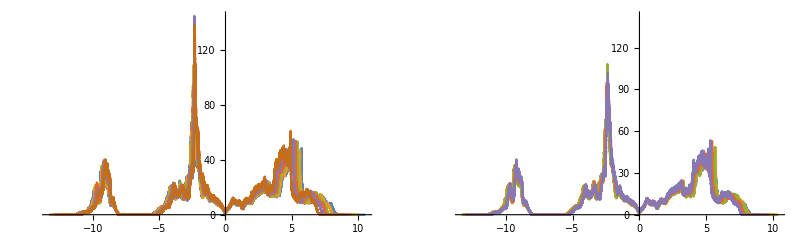

```mathematica
(*Increasing the smearing has very little effect on the band relaxation*)
GraphicsGrid[{{ListLinePlot[perfDOS,PlotRange->All],ListLinePlot[perfDOSM,PlotRange->All]}}]
```

```mathematica
Extract a window for moving averages of DOS;
```

```mathematica
(*To get an electronic DOS function, do moving average over some window, then interpolate cubic hermite polynomila*)
(*Let the smearing window be determined by the electronic temperature*)
smearingeV[window_]:=(window/(perfDOSM[[1]]//Length))*(-perfDOSM[[1]][[1]][[1]]+perfDOSM[[1]][[-1]][[1]])
windoweV[smearing_]:=(perfDOSM[[1]]//Length)*smearing/(-perfDOSM[[1]][[1]][[1]]+perfDOSM[[1]][[-1]][[1]])
smearingK[window_]:=(window/(perfDOSM[[1]]//Length))*(-perfDOSM[[1]][[1]][[1]]+perfDOSM[[1]][[-1]][[1]])/K2eV
windowK[smearing_]:=(perfDOSM[[1]]//Length)*smearing/(-perfDOSM[[1]][[1]][[1]]+perfDOSM[[1]][[-1]][[1]])*K2eV
windoweV[0.026];
windowK[300];
windows=Table[windowK[temps2[[i]]],{i,1,7}]
Floor@windows
(*IMPORTANT - double check the temperature and volumes correspond to plain QHA - mermin-QHA should be fine*)
```

{19.002,19.002,48.1383,120.346,158.35,202.688,240.691}

{19,19,48,120,158,202,240}

```mathematica
Interpolate moving averaged DOS;
```

```mathematica
(*Check moving average over different windows - 50 is fine*)
inter1=Interpolation[MovingAverage[perfDOSM[[1]],1],Method->"Hermite",InterpolationOrder->3];
inter5=Interpolation[MovingAverage[perfDOSM[[1]],5],Method->"Hermite",InterpolationOrder->3];
inter10=Interpolation[MovingAverage[perfDOSM[[1]],10],Method->"Hermite",InterpolationOrder->3];
inter50=Interpolation[MovingAverage[perfDOSM[[1]],50],Method->"Hermite",InterpolationOrder->3];
inter100=Interpolation[MovingAverage[perfDOSM[[1]],100],Method->"Hermite",InterpolationOrder->3];
```

```mathematica
interFixed=Table[Interpolation[MovingAverage[perfDOSM[[i]],Floor@windows[[1]]],Method->"Hermite",InterpolationOrder->3],{i,1,7}];
interMoving=Table[Interpolation[MovingAverage[perfDOSM[[i]],Floor@windows[[i]]],Method->"Hermite",InterpolationOrder->3],{i,1,7}];
```

```mathematica
Plot interpolated moving averaged DOS;
```

```mathematica
GraphicsGrid[{{Plot[Evaluate@Table[interMoving[[i]][x]+i,{i,1,7}],{x,-5,5},PlotRange->All,PlotLegends->SwatchLegend[Table[temps2[[i]],{i,1,7}]],ImageSize->450],Plot[Evaluate@Table[interFixed[[i]][x]+i,{i,1,7}],{x,-5,5},PlotRange->All,PlotLegends->SwatchLegend[Table[temps2[[i]],{i,1,7}]],ImageSize->450]}},ImageSize->1020]
```

-Graphics-

#### Import conductivity;

```mathematica
(*Mermin+QHA*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/OUT_ZrC_Mermin_QHA_PERF_KP191919"];
filesTRACEperfMermin={"4667_000_000.hte.trace", "4667_000_026.hte.trace", "4671_300_026.hte.trace", "4685_760_065.hte.trace", "4731_1900_164.hte.trace", "4760_2500_215.hte.trace", "4802_3200_276.hte.trace", "4848_3800_327.hte.trace"};
(*Exclude the DOS with zero smearing*)
importedTRACEperfMermin=Table[ReadList[filesTRACEperfMermin[[i]],{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,2,8}];
(*QHA*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/OUT_ZrC_QHA_fixedTel_PERF_KP191919"];
filesTRACEperf={"46583_SP_COND_252525.hte.trace", "4685_SP_COND_252525.hte.trace", "4730_SP_COND_252525.hte.trace", "4759_SP_COND_252525.hte.trace", "4801_SP_COND_252525.hte.trace", "4850_SP_COND_252525.hte.trace"};
importedTRACEperf=Table[ReadList[filesTRACEperf[[i]],{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,6}];
```

```mathematica
importedTRACEperf[[1]][[1]]
```

{-0.00001,40.,-0.134371,103.623,-2.30047×10^-6,4.40255×10^19,-2.81794×10^-9,4.40966×10^13,0.362406,1.54701×10^-9}

```mathematica
Parse conductivity;
```

```mathematica
importedDOSperfMermin[[1]][[1]]
```

{-0.97668455E+00,0.00000000E+00,0.00000000E+00}

```mathematica
(*# Ef[Ry] T[K] N DOS(Ef) S s/t R_H kappa0 c chi*)
(*Mermin+QHA*)
perfSIGMAMoTau=Table[Table[{importedTRACEperfMermin[[k]][[i]][[2]],importedTRACEperfMermin[[k]][[i]][[6]]},{i,1,importedTRACEperfMermin[[k]]//Length}][[1;;100]],{k,2,7}];
perfKAPPAMoTau=Table[Table[{importedTRACEperfMermin[[k]][[i]][[2]],importedTRACEperfMermin[[k]][[i]][[8]]},{i,1,importedTRACEperfMermin[[k]]//Length}][[1;;100]],{k,2,7}];
```

```mathematica
perfSIGMAoTau=Table[Table[{importedTRACEperf[[k]][[i]][[2]],importedTRACEperf[[k]][[i]][[6]]},{i,1,importedTRACEperf[[k]]//Length}][[1;;100]],{k,1,6}];
perfKAPPAoTau=Table[Table[{importedTRACEperf[[k]][[i]][[2]],importedTRACEperf[[k]][[i]][[8]]},{i,1,importedTRACEperf[[k]]//Length}][[1;;100]],{k,1,6}];
```

```mathematica
ListPlot[{perfSIGMAMoTau[[6]],perfSIGMAoTau[[6]]}]
ListPlot[{perfKAPPAMoTau[[6]],perfKAPPAoTau[[6]]}]
```

-Graphics-

-Graphics-

```mathematica
interSIGMAMoTau=Table[Interpolation[perfSIGMAMoTau[[i]]],{i,1,6}];
interKAPPAMoTau=Table[Interpolation[perfKAPPAMoTau[[i]]],{i,1,6}];
interSIGMAoTau=Table[Interpolation[perfSIGMAoTau[[i]]],{i,1,6}];
interKAPPAoTau=Table[Interpolation[perfKAPPAoTau[[i]]],{i,1,6}];
```

```mathematica
temps3
```

{300,760,1900,2500,3200,3800}

```mathematica
GraphicsGrid[{{Plot[Evaluate@Table[interSIGMAMoTau[[i]][t],{i,1,6}],{t,100,1500},ImageSize->400,PlotLegends->SwatchLegend[Table[temps3[[i]],{i,1,6}]]],Plot[Evaluate@Table[interSIGMAoTau[[i]][t],{i,1,6}],{t,100,1500},ImageSize->400,PlotLegends->SwatchLegend[Table[temps3[[i]],{i,1,6}]]]}},ImageSize->1000]
GraphicsGrid[{{Plot[Evaluate@Table[interKAPPAoTau[[i]][t],{i,1,6}],{t,100,1500},ImageSize->400,PlotLegends->SwatchLegend[Table[temps3[[i]],{i,1,6}]]],Plot[Evaluate@Table[interKAPPAoTau[[i]][t],{i,1,6}],{t,100,1500},ImageSize->400,PlotLegends->SwatchLegend[Table[temps3[[i]],{i,1,6}]]]}},ImageSize->1000]
```

-Graphics-

```mathematica
PlotStyle->Gray,Frame->True,FrameLabel->{"T (K)","τ (s)"},ImageSize->500],ListPlot[{tmean55tau,tmean55tauFD},PlotLegends->SwatchLegend[{"τ","τ_FD"}]]
```

```mathematica
(*Make sigma including tau*)
(*tmean55tauinter=Interpolation[tmean55tau,InterpolationOrder->6];
tmean55tauFDinter=Interpolation[tmean55tauFD,InterpolationOrder->6];*)
interSIGMAM=Table[interSIGMAMoTau[[i]][t]*tmean55tauinter[t],{i,1,6}];
interSIGMAMFD=Table[interSIGMAMoTau[[i]][t]*tmean55tauFDinter[t],{i,1,6}];
interSIGMAMfixTau300=Table[interSIGMAMoTau[[i]][t]*tmean55tauinter[300],{i,1,6}];
(*Make kappa including tau*)
interKAPPAM=Table[interKAPPAMoTau[[i]][t]*tmean55tauinter[t],{i,1,6}];
interKAPPAMFD=Table[interKAPPAMoTau[[i]][t]*tmean55tauFDinter[t],{i,1,6}];
interKAPPAMfixTau300=Table[interKAPPAMoTau[[i]][t]*tmean55tauinter[300],{i,1,6}];
```

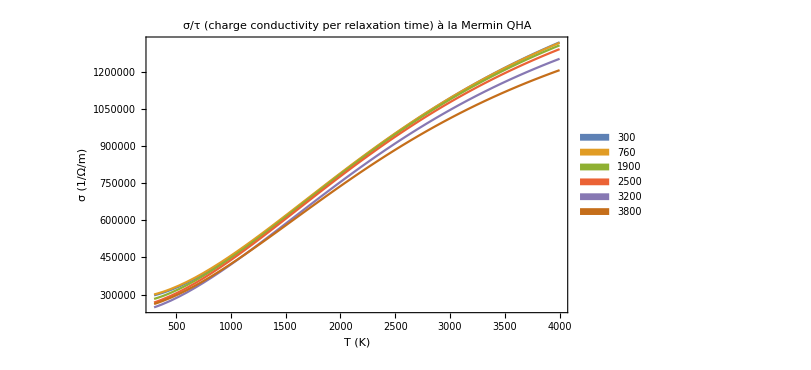

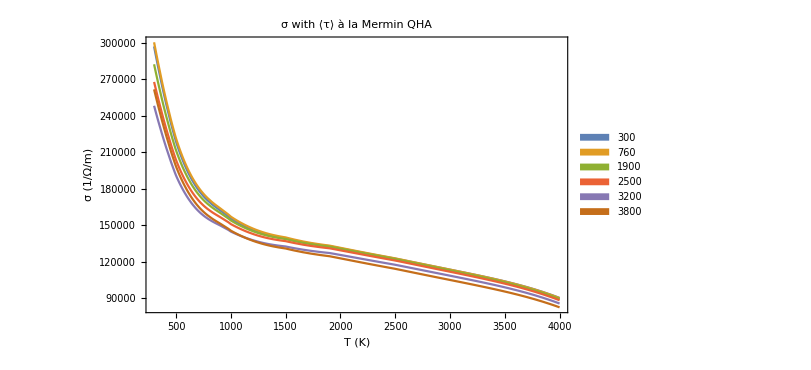

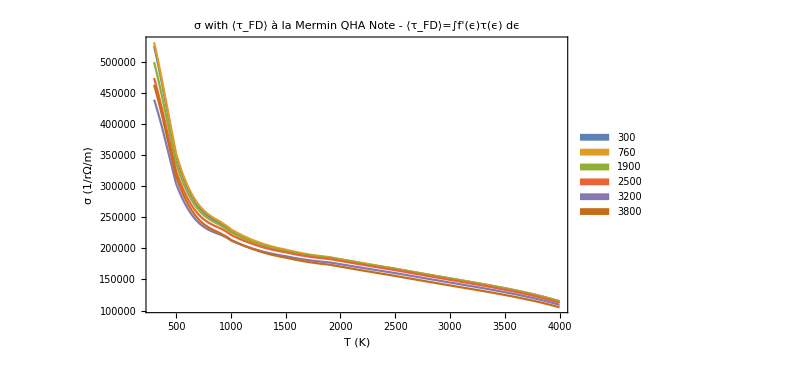

```mathematica
Plot[Evaluate@interSIGMAMfixTau300,{t,300,4000},PlotRange->All,PlotLegends->SwatchLegend[temps3],Frame->True,FrameLabel->{"T (K)","σ (1/Ω/m)"},ImageSize->600,PlotLabel->"σ/τ (charge conductivity per relaxation time) à la Mermin QHA"]
Plot[Evaluate@interSIGMAM,{t,300,4000},PlotRange->All,PlotLegends->SwatchLegend[temps3],Frame->True,FrameLabel->{"T (K)","σ (1/Ω/m)"},ImageSize->600,PlotLabel->"σ with ⟨τ⟩ à la Mermin QHA"]
Plot[Evaluate@interSIGMAMFD,{t,300,4000},PlotRange->All,PlotLegends->SwatchLegend[temps3],Frame->True,FrameLabel->{"T (K)","σ (1/rΩ/m)"},ImageSize->600,PlotLabel->"σ with ⟨τ_FD⟩ à la Mermin QHA \n Note - ⟨τ_FD⟩=∫f'(ϵ)τ(ϵ) dϵ"]
```

```mathematica
w
```

```mathematica
Plot[Evaluate@interSIGMAM,{t,100,1500},PlotRange->All,PlotLegends->SwatchLegend[temps3]]
Plot[Evaluate@interSIGMAMfixTau300,{t,100,1500},PlotRange->All,PlotLegends->SwatchLegend[temps3]]
Plot[Evaluate@interSIGMAMFD,{t,100,1500},PlotRange->All,PlotLegends->SwatchLegend[temps3]]
```

-Graphics-

-Graphics-

-Graphics-

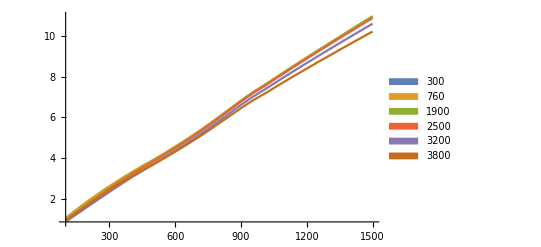

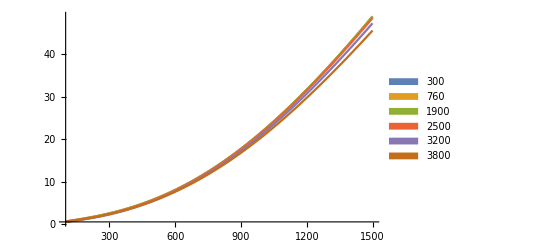

```mathematica
Plot[Evaluate@interKAPPAM,{t,100,1500},PlotRange->All,PlotLegends->SwatchLegend[temps3]]
Plot[Evaluate@interKAPPAMfixTau300,{t,100,1500},PlotRange->All,PlotLegends->SwatchLegend[temps3]]
```

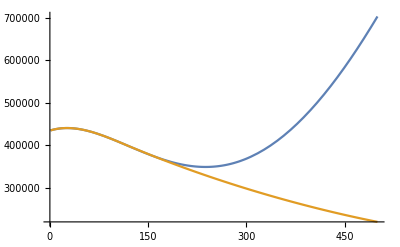

```mathematica
Plot[{Evaluate[PadeApproximant[interSIGMAM[[1]],{t,100,4}]],interSIGMAM[[1]]},{t,1,500}]
```

1.04322×10^-14-1.72671×10^-17 x+1.18302×10^-20 x^2-3.48646×10^-24 x^3+3.65368×10^-28 x^4

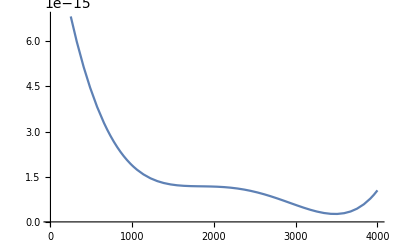

```mathematica
tmean55tauFit=Fit[tmean55tau,{1,x,x*x,x*x*x,x*x*x*x},x]
Plot[tmean55tauFit,{x,1,4000}]
```